# Knot for Sail aka Boats Mah Goats

```mathematica
ClearAll[f]
```

```mathematica
BoatCurve = (3x^2/23);

BoatDensity = .3; (*g/ml*)
MassBalast = 250 ;  (*g*)
COBallast = {0,0};

MastMass = 96; (*g*)
MastCom = {0, 25};

BoatLength = 45;
BoatWidth = 20;
BoatHeight = 13;

xbd = x/.FindRoot[BoatHeight-BoatCurve, {x, 10}]


boat = ImplicitRegion[BoatCurve<y<BoatHeight,{{x,-xbd,xbd},{y,-2,BoatHeight}}];
water = ImplicitRegion[y<d,{{x,-xbd,xbd},{y,-2,BoatHeight}}];
under = RegionIntersection[boat,water];

totalMass = N[BoatLength*Integrate[BoatDensity,{x,y}∈boat]+MassBalast+MastMass]
mass = N[BoatLength*Integrate[BoatDensity,{x,y}∈boat]]
disp = BoatLength*Integrate[.997,{x,y}∈under];

com = 1/totalMass*(RegionCentroid[boat]*mass+MassBalast*COBallast+MastMass*MastCom)

Show[RegionPlot[{water/.{d->5}, boat, under/.{d->5}}, AspectRatio->Automatic], ListPlot[{com}]]

com = Append[com, 0];
```

9.98332

2682.1

2336.1

{0.,7.68859}

-Graphics-

```mathematica
Torque[theta_]:=Module[{},
boat = ImplicitRegion[BoatCurve<y<BoatHeight,{{x,-xbd,xbd},{y,-2,BoatHeight}}];
water = ImplicitRegion[If[theta<90,y<Tan[theta Degree]*x+d,y>Tan[theta Degree]*x+d],{{x,-xbd,xbd},{y,-2,BoatHeight}}];

under = RegionIntersection[boat,water];
disp = .997*10*RegionMeasure[under];
draft = N[d/.FindRoot[disp==mass,{d,-30,30},AccuracyGoal->3][[1]], 3];
cob = Append[RegionCentroid[under/.{d->draft}],0];
buoyancy = mass*98/10*{-Sin[theta Degree],Cos[theta Degree],0};
torque = Cross[cob-com,buoyancy][[3]];
torque
]
```

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[-9.98332≤x≤9.98332&&-2≤y<13&&d+x Tan[20 °]>y&&3 x^2<23 y,{x,y}].

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

872.318

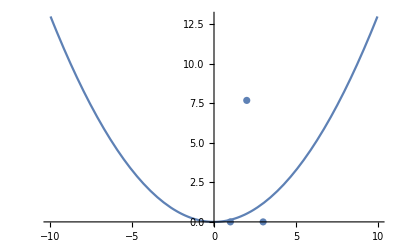

```mathematica
Torque[20]

Show[Plot[BoatCurve, {x,-xbd,xbd}, PlotRange->{{-xbd,xbd},{0,BoatHeight}}],Plot[Tan[HeelAngle Degree]*(x)+draft, {x, -xbd,xbd}], ListPlot[{com}]]
```

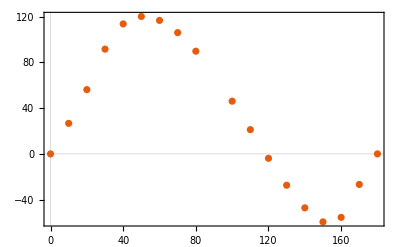

```mathematica
ListPlot[Table[{theta,Torque[theta]},{theta,{0,10,20,30,40,50,60,70,80,100,110,120,130,140,150,160,170,180}}], PlotTheme->"Scientific"]
```